# Hunt the Wumpus

Create a simple implementation of the classic textual game Hunt The Wumpus.

The game is set in a cave that consists of a 20 room labyrinth. 
Each room is connected to 3 other rooms (the cave is modeled after the vertices of a dodecahedron). 
The objective of the player is to find and kill the horrendous beast Wumpus that lurks in the cave.

The player has 5 arrows. If they run out of arrows before killing the Wumpus, the player loses the game.

In the cave are:

One Wumpus

Two giant bats

Two bottomless pits

If the player enters a room with the Wumpus, he is eaten by it and the game is lost.

If the player enters a room with a bottomless pit, he falls into it and the game is lost.

If the player enters a room with a giant bat, the bat takes him and transports him into a random empty room.

Each turn the player can either walk into an adjacent room or shoot into an adjacent room.

Whenever the player enters a room, he “senses” what happens in adjacent rooms. The messages are:

Nearby Wumpus: “You smell something terrible nearby.”

Nearby bat: “You hear a rustling.”

Nearby pit: “You feel a cold wind blowing from a nearby cavern.”

When the player shoots, he wins the game if he is shooting in the room with the Wumpus. If he shoots into another room, the Wumpus has a 75% of chance of waking up and moving into an adjacent room: if this is the room with the player, he eats him up and the game is lost.

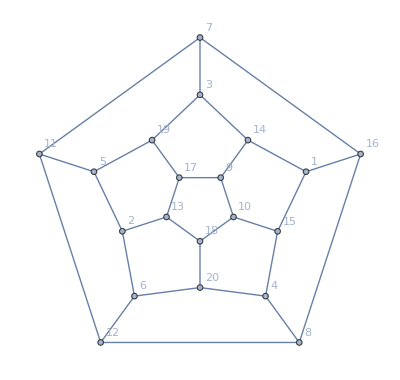

```mathematica
graph=AdjacencyGraph[
{{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0},{0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0}}, VertexCoordinates->{{1.548,0.503},{-1.134,-0.368},{0.,1.628},{0.957,-1.317},{-1.548,0.503},{-0.957,-1.317},{0.,2.466},{1.449,-1.995},{0.302,0.416},{0.489,-0.159},{-2.345,0.762},{-1.45,-1.995},{-0.489,-0.159},{0.7,0.965},{1.133,-0.369},{2.345,0.762},{-0.302,0.416},{0.,-0.514},{-0.7,0.965},{0.,-1.192}},VertexLabels->Automatic]
```

```mathematica
(*
DynamicModule[
{v=RandomInteger[{1,20}],playeralive=True,wumpusalive=True,
newgraph=graph,
arrows=5,bool,shooting=True,
loc,wumpus,bat1,bat2,pit1,pit2,
buttons,pressed=False,
adjVec,messageAssociation,messageDone,
message="",message2=""},
{wumpus,bat1,bat2,pit1,pit2}=RandomSample[Range[20],5];

(*This boolean is used to to figure out when the game ends*)
bool:=wumpusalive||arrows>0||!playeralive;

(*These dynamic panes provide the main messages after events*)
Print[Column@{Panel[Dynamic[message]],Panel[Dynamic[message2]],Panel["Arrows: "Dynamic[arrows]]}];
Print[Dynamic[newgraph]];
(*The messageAssociation just translates the numbers given into a message in the panels*)
messageAssociation=<|
wumpus->"You smell something terrible nearby.",
bat1->"You hear a rustling.",
bat2->"You hear a rustling.",
pit1->"You feel a cold wind blowing from a nearby cavern.",
pit2->"You feel a cold wind blowing from a nearby cavern."|>;

While[bool,
adjVec=AdjacencyList[graph,v];
messageDone=Select[adjVec/.messageAssociation,!NumericQ[#]&];
If[VectorQ[messageDone,NumericQ],message="This room feels neutral",
message=Column@messageDone];

(*Creates the graph*)
newgraph=HighlightGraph[graph,{Style[adjVec,Green],Style[v,Red]}];

(*Modifies the dialog and processes different occurences*)
message2="Where would you like to shoot your arrow?";
buttons=Button[#,

If[shooting,
(* NEED TO DO 
x Message dialog for shooting in the room
X check if the WUMPUS is in that room (if so the WIN)
X If the room has a bat then the bat is dead
X If the WUMPUS is nearby, it has a 75% chance to go to one of the rooms adjacent to it
*)
message="You shot into room " <> ToString[#];
(*WUMPUS check*)
If[#==wumpus,wumpusalive=False;message="You killed the WUMPUS";,
If[MemberQ[adjVec,wumpus]&&RandomChoice[{0.75,0.25}->{True,False}],
wumpus=RandomChoice[AdjacencyList[graph,wumpus]];
If[wumpus==v,message="You have been EATEN."]
]];
(*BAT check*)
If[#==bat1,bat1=0;message="You killed a BAT";];
If[#==bat2,bat2=0;message="You killed a BAT";];

message2="Where would you like to move?";arrows--;,

(*Movement*)
(*NEED TO DO 
X Player movement
·If WUMPUS -> DEAD
·If HOLE -> DEAD
·If BAT -> Randomly moved 
*)
v=#;
If[MemberQ[{bat1,bat2},v],v=RandomInteger[{1,20}];
message="You have been flown to "<>ToString[v]<>"."];
If[wumpus==v,message="You have been EATEN.";playeralive=False];
If[MemberQ[{pit1,pit2},v],message="You have FALLEN.";playeralive=False];
shooting=!shooting;
]]&/@adjVec;
If[shooting,
shooting=!shooting;
Row@Append[buttons,
Button["Don't shoot",message2="Where would you like to move?";message="You didn't shoot"]],
Row@buttons
]//Print;
]
]
```

## Modified

```mathematica
DynamicModule[
{v=RandomInteger[{1,20}],playeralive=True,wumpusalive=True,
newgraph=graph,nextTurn=True,color=Red,
arrows=5,bool,shooting=True,
loc,wumpus,bat1,bat2,pit1,pit2,
shootingButtons="",movingButtons="",
buttons="",pressed=False,layout,
adjVec,messageAssociation,messageDone,
message="Let's begin",message2=""},
{wumpus,bat1,bat2,pit1,pit2}=RandomSample[Range[20],5];

(*This boolean is used to to figure out when the game ends*)
bool:=wumpusalive&&arrows>0&&playeralive;
Print[bool];
(*The messageAssociation just translates the numbers given into a message in the panels*)
messageAssociation=<|
wumpus->"You smell something terrible nearby.",
bat1->"You hear a rustling.",
bat2->"You hear a rustling.",
pit1->"You feel a cold wind blowing from a nearby cavern.",
pit2->"You feel a cold wind blowing from a nearby cavern."|>;

(*Creates a layout *)
layout=Column[
{Dynamic@color,
Dynamic@message,Dynamic@message2,
"Arrows: " <>ToString[ Dynamic[arrows]],
Dynamic@Row@buttons,Dynamic@newgraph}
];

Print[layout];

While[bool,

If[nextTurn,
nextTurn=False;

adjVec=AdjacencyList[graph,v];
messageDone=Select[adjVec/.messageAssociation,!NumericQ[#]&];
If[VectorQ[messageDone,NumericQ],message="This room feels neutral",
message=Column@messageDone];

(*Creates the graph*)
newgraph=HighlightGraph[graph,{Style[adjVec,Green],Style[v,Red]}];

(*Modifies the dialog and processes different occurences*)
message2="Where would you like to shoot your arrow?";

shootingButtons=Button[#,

(* NEED TO DO 
x Message dialog for shooting in the room
X check if the WUMPUS is in that room (if so the WIN)
X If the room has a bat then the bat is dead
X If the WUMPUS is nearby, it has a 75% chance to go to one of the rooms adjacent to it
*)
message="You shot into room " <> ToString[#];
(*WUMPUS check*)
If[#==wumpus,wumpusalive=False;message="You killed the WUMPUS";,
If[MemberQ[adjVec,wumpus]&&RandomChoice[{0.75,0.25}->{True,False}],
wumpus=RandomChoice[AdjacencyList[graph,wumpus]];
If[wumpus==v,message="You have been EATEN."]
]];
(*BAT check*)
If[#==bat1,bat1=0;message="You killed a BAT";];
If[#==bat2,bat2=0;message="You killed a BAT";];

shooting=False;
color=Green;
Print[shooting];
message2="Where would you like to move?";arrows--;
]&/@adjVec;


movingButtons=Button[
(*Movement*)
(*NEED TO DO 
X Player movement
·If WUMPUS -> DEAD
·If HOLE -> DEAD
·If BAT -> Randomly moved 
*)
v=#;
If[MemberQ[{bat1,bat2},v],v=RandomInteger[{1,20}];
message="You have been flown to "<>ToString[v]<>"."];
If[wumpus==v,message="You have been EATEN.";playeralive=False];
If[MemberQ[{pit1,pit2},v],message="You have FALLEN.";playeralive=False];
shooting=True;
nextTurn=True;
]&/@adjVec;

If[shooting,
buttons=Append[shootingButtons,
Button["Don't shoot",shooting=False;message2="Where would you like to move?";message="You didn't shoot"]];,
buttons=movingButtons;
];
]

]
]
```

True

Arrows: Dynamic[arrows$81596]

```mathematica
Counts@Table[RandomChoice[{0.75,0.25}->{True,False}],100]
```

<|True→75,False→25|>

```mathematica
Manipulate[If[running,x++,x],
{{x,0},ControlType->None},
{{running,True},ControlType->None},
Button["play",running=True],Button["stop",running=False]]
```